```mathematica
data=Import["/Users/matt/GitHub Clones/CircuitPlayground/AllSensorsSaveData/values.csv"]
```

{{x,y,z,leftButton,rightButton,lightSensor,soundSensor,tempSensor},{null},{0.17,4.27,8.09,0.,0.,62.,343.,76.17},{0.47,3.84,7.87,0.,0.,81.,344.,76.17},{0.69,1.14,9.94,0.,0.,64.,343.,76.17},{0.73,0.51,10.24,0.,0.,64.,341.,76.17},49988,{null},{null},{null},{null},{null},{null}}
 |  |  |  |

```mathematica
data=Select[data,Length[#]==8&];
data=Dataset[Map[AssociationThread[First[data],#]&,Rest[data]]]
```

Dataset[<>]

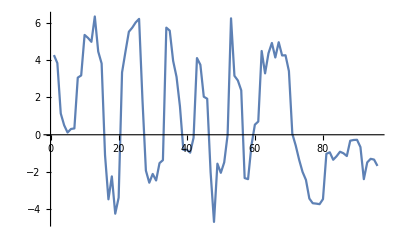

```mathematica
ListLinePlot[Normal[data[All,"y"]]]
```

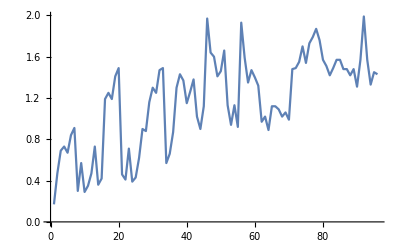

```mathematica
ListLinePlot[Normal[data[All,"x"]]]
```

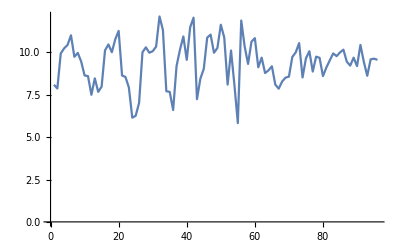

```mathematica
ListLinePlot[Normal[data[All,"z"]]]
```